```mathematica
LaunchKernels[10]
```

{Local (10),Local (10),Local (10),Local (10),Local (10),Local (10),Local (10),Local (10),Local (10),Local (10)}

```mathematica
(*Parameters: many are not used, just there to remind me what I am doing...*)
l=1;
M=1;
mpi=1;
α=10;
N0=100; 
qMax=18.00; (*UV Cutoff*)
qGrid=Subdivide[0.001,qMax,N0-1];
Δq=(qMax)/(N0-1);
```

```mathematica
(*Potential Functions: Construct from some V(r) or other...*)
(*V[p_,q_]:=1/(Pi^2)*α/mpi^3*1/((1+(p+q)^2/mpi^2)*(1+(p-q)^2/mpi^2));*)
V[p_,q_]:=-α/(8*Pi^1.5*mpi)*1/(p*q)*(Exp[-1/(4*mpi^2)*(p-q)^2]-Exp[-1/(4*mpi^2)*(p+q)^2]); (*V(r)=-α e^(-m^2r^2) with l = 0*)
(*V[p_,q_]:=-α*Exp[-1/4*(p+q)^2]*(2+p*q+(p*q-2)*Exp[p*q])/(8p^2*q^2*Pi^1.5); (*V(r)=-α e^(-r^2) with l = 1*)*)
(*V[p_,q_]:=-(α/(16*Pi^1.5*mpi^3))*Exp[-1/(4mpi^2)*(p+q)^2]*(p*q/(2mpi^2))^(-2)(Sinh[p*q/(2mpi^2)]-p*q/(2mpi^2)*Cosh[p*q/(2mpi^2)]); (*V(r)=-α e^(-m^2r^2)*)*)
```

```mathematica
(*Construct the Kernel and inhomogeneous piece*)
gvec[u_]:=4Pi*Table[qGrid[[i]]^2*Δq*1/(u^2-(qGrid[[i]]^2)),{i,N0}];
Vmat=Table[V[qGrid[[i]],qGrid[[j]]],{i,N0},{j,N0}];
Kmat[z_]:=Vmat.DiagonalMatrix[gvec[z]];
```

0.30154676566998533938

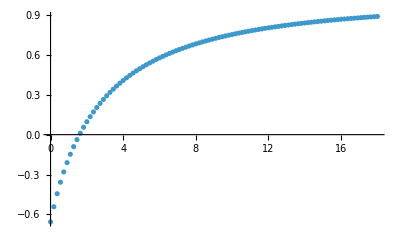

```mathematica
z0=-3;
SetPrecision[Det[IdentityMatrix[N0]-Kmat[z0]],20]

BSExpr := SetPrecision[Det[IdentityMatrix[N0]-Kmat[z]],20];
zGrid = (I*qGrid);
BSExprPts = ParallelTable[{Im[z],BSExpr},{z,zGrid}]; (* To create plot on the Ip plane (takes the Imaginary component of z to allow plotting in mathematica)*)
ListPlot[BSExprPts,PlotRange->{All,Automatic}]

(*Iterate over a list of real negative z values and plot to search for bound states*)
```

InterpolatingFunction::dmval: Input value {0.000367714} lies outside the range of data in the interpolating function. Extrapolation will be used.

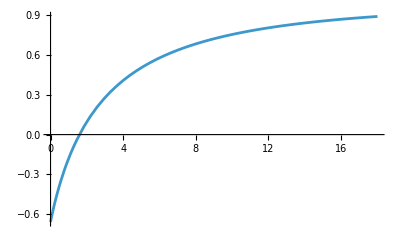

{x→1.59488}

```mathematica
BSExprInterp = Interpolation[BSExprPts];
Plot[BSExprInterp[x],{x,0,qMax},PlotRange->{All,Automatic}]
FindRoot[BSExprInterp[x]==0 ,{x,2}]
```

```mathematica
SetPrecision[Det[IdentityMatrix[N0]-Kmat[I*2]],20]
```

0.096831154465322796798

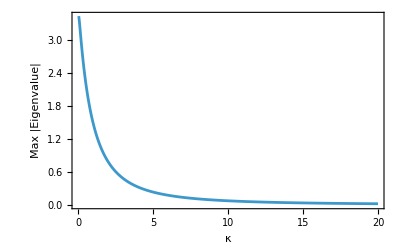

General::munfl: 2.22664×10^-203 1.51213×10^-222 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.08948×10^-224 9.11409×10^-225 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.88011×10^-203 1.65107×10^-222 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Eigenvalues::eival: Unable to find all roots of the characteristic polynomial.

FindRoot::nveq: The number of equations does not match the number of variables in FindRoot[f[κ],{κ,1.}].

ReplaceAll::reps: {FindRoot[f[κ],{κ,1.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Eigenvalues::eival: Unable to find all roots of the characteristic polynomial.

FindRoot::nveq: The number of equations does not match the number of variables in FindRoot[f[κ],{κ,1.}].

ReplaceAll::reps: {FindRoot[f[κ],{κ,1.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

κ/.FindRoot[f[κ],{κ,1.}]

General::munfl: 1.81644×10^-203 1.45466×10^-222 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.86714×10^-225 4.01772×10^-225 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.69691×10^-203 1.43478×10^-222 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

```mathematica
(*(* Separate weights and propagator for clarity *)
Wvec = 4 Pi qGrid^2 Δq;
G0Vec[u_] := 1/(u^2 - qGrid^2);           (* pass u = I κ for bound states *)
Kmat[u_] := Vmat . DiagonalMatrix[Wvec*G0Vec[u]];*)

(* Scan κ to see where the largest eigenvalue crosses 1 *)
kappaList = N@Range[0.05, 20.0, 0.01];
rhoList = Table[
   Max[Abs@Eigenvalues[Kmat[I κ], 20]], {κ, kappaList}];

ListLinePlot[Transpose@{kappaList, rhoList},
 Frame -> True, FrameLabel -> {"κ", "Max |Eigenvalue|"},
 PlotRange -> All]

(* Define f(κ) = ρ(κ) - 1 and root-find near a crossing κ0 *)
f[κ_] := Module[{vals = Eigenvalues[Kmat[I κ], 20]},
   Max[Abs@vals] - 1
];
κB = κ /. FindRoot[f[κ], {κ, 1.0}]  (* pick a good initial guess from the plot *)
EB = -κB^2;                         (* binding energy in these units *)
```